```mathematica
ClearAll["Global`*"]
```

## BaTiO_3:

### Thin film free energy

Free energy of a thin film with dependencies on misfit strain, electrostrictive tensor, and elastic modulii

```mathematica
Gfilmf[α1t_,α11t_,α111_,aE_,Gelt_,P_]:= α1t P^2+ α11t P^4+ α111 P^6- aE P + Gelt
```

```mathematica
Gfilmt[α1_,um_,Q12_,Ct_,α11_,α111_,aE_,P_]:=Gfilmf[α1-2um Q12 Ct,α11+Q12^2 Ct,α111,aE,um^2 Ct,P]
```

```mathematica
Gfilmtc[α1_,um_,Q12_,C11_,C12_,α11_,α111_,aE_,P_]:=Gfilmt[α1,um,Q12,C11+C12-(2 C12^2)/C11,α11,α111,aE,P]
```

```mathematica
Gfilmtc[α1,um,Q12,C11,C12,α11,α111,aE,P]
```

-aE P+(C11+C12-(2 C12^2)/C11) um^2+P^2 (-2 (C11+C12-(2 C12^2)/C11) Q12 um+α1)+P^4 ((C11+C12-(2 C12^2)/C11) Q12^2+α11)+P^6 α111

Inputting the coefficients for BaTiO_3 to get the free energy as a function of misfit strain, applied field, polarization, and temperature.

```mathematica
GfilmFE[um_,aE_,P_,T_]:=Gfilmtc[(T-383)/(2 (1.7*10^5) (8.85*10^-12)),um,-0.043,1.75*10^11,8.46*10^10,3.6(T-448)*10^6,6.6*10^9,aE,P]
```

At this point, we can’t take a derivative with respect to polarization and solve for polarization analytically. We have to abandon symbolic math at this point. We need to take the above expression and solve it numerically in order to get the curves in Fig 6. But let’s start with Fig 5. We can first pick um = -0.01% and then a specific field curve to get the polarization.

```mathematica
plotFont={FontWeight->"Bold",FontSize->24};
```

## Polarization as a function of applied electric and strain fields

```mathematica
sol[um_,aE_,T_]:=NSolve[{D[GfilmFE[um,aE,P,T],P]==0,P>0},P]
```

```mathematica
plotFont={FontWeight->"Bold",FontSize->20};Manipulate[ListLinePlot[{Table[{T,P/.Flatten[sol[um,0,T]]},{T,320,450,1}],Table[{T,P/.Flatten[sol[um,10*10^5,T]]},{T,320,450,1}],Table[{T,P/.Flatten[sol[um,35*10^5,T]]},{T,320,450,1}]},Frame->True,FrameLabel->{"T [K]","P [C/m^2]"},BaseStyle->plotFont,ImageSize->800,PlotStyle->{{Blue,Dashing[Tiny],Thickness[0.0025]},{Blue,Dashing[Large],Thickness[0.0025]},{Blue,Thickness[0.0025]}},PlotLegends->Placed[{"E = 0 [kV/cm]","E = 10 [kV/cm]","E = 35 [kV/cm]"},{Scaled[{0.8,0.935}],{0.8,0.935}}],LabelStyle->Directive[Black,Bold]],{um,-0.001,0.001}]
```

ReplaceAll::reps: {sol[0, 0, 320]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {sol[0, 0, 321]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {sol[0, 0, 322]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {sol[0, 0, 320]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {sol[0, 0, 321]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {sol[0, 0, 322]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {sol[0, 0, 320]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {sol[0, 0, 321]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {sol[0, 0, 322]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {sol[0, 0, 320]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {sol[0, 0, 321]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {sol[0, 0, 322]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {sol[0, 0, 320]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {sol[0, 0, 321]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {sol[0, 0, 322]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Now here is the tricky part. Let’s solve for ΔC_(E,σ) as a function of temperature to match d, e,f from Fig 6. We can’t approach this the same way because we need to solve for polarization at some given applied field and temperature and put this back into our free energy with those same temperature and applied fields.

## Entropy and heat capacity

```mathematica
ϕ=1;equilibFE=ParallelTable[Table[Table[{Solve[{D[GfilmFE[um,aE,P,T],P]==0,P∈Reals,P>0},P],aE,T,um},{T,1,580,ϕ}],{aE,0*10^5,150*10^5,1*10^5}],{um,-0.001,0.001,0.001}]; Dimensions[equilibFE]
```

{3,151,580,4}

```mathematica
ϕ=1;
```

```mathematica
Export["/home/john/projects/equilibPolFE.csv",equilibFE]
```

/home/john/projects/equilibPolFE.csv

We have built a A[j, k, l,m] object that describes the equilibrium polarization in this parameter space {j,k,l} which correspond to strain, electric field and temperature. m corresponds to the number of polarization solutions. Note that not all of them are physical. The below function computes the free energy as we vary j, k, or l (l changes the temperature).

```mathematica
G0filmFE[j_,k_,l_]:=GfilmFE[equilibFE[[j,k,l,4]],equilibFE[[j,k,l,2]],P/.equilibFE[[j,k,l,1]],equilibFE[[j,k,l,3]]]
```

The excess entropy, which is defined as S(T) = -(∂G0)/(∂T) at constant field, can be found by considering the numerical approximation to the derivative f’[x] = (f[x+h] - f[x] )/h. This is where one needs to be careful. Different approximations for derivatives can give radically different answers. The forward differentiation is OK here for S(T) but other derivatives can be problematic. It seems backward is the most useful(perhaps since we are doing a forward sum and

```mathematica
S[j_,k_,l_]:=Flatten[-(G0filmFE[j,k,l+1]-G0filmFE[j,k,l])/ϕ]
```

Similarly, we have the heat capacity, in which we use the second derivative approximation f''[x] =((f[x+h] - f[x])/h-(f[x] - f[x-h])/h)/h= (f[x+h] - 2 f[x] + f[x-h])/h^2

```mathematica
ΔCBackward[j_,k_,l_]:=-equilibFE[[j,k,l,3]]*((G0filmFE[j,k,l]-2G0filmFE[j,k,l-1]+G0filmFE[j,k,l-2])/(ϕ)^2);
```

### Entropy plot:

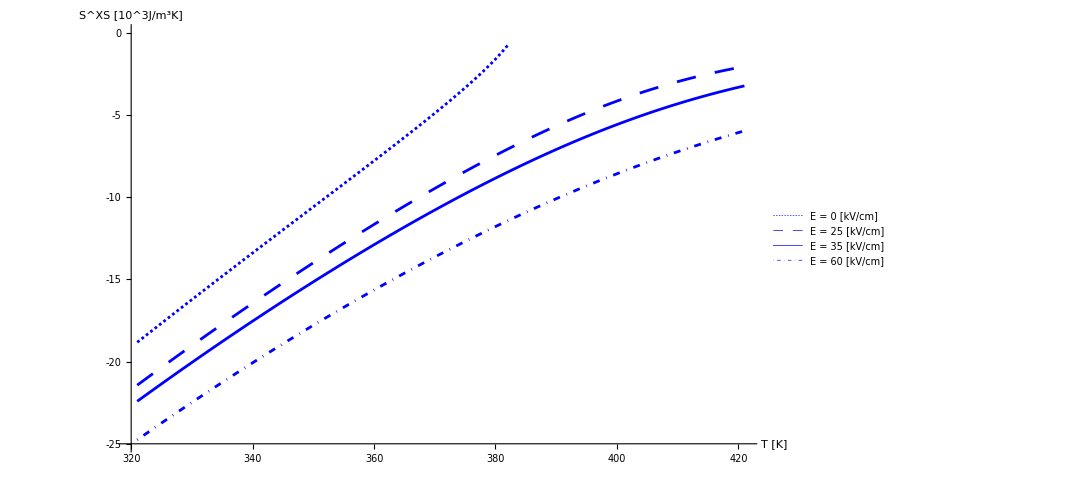

```mathematica
ListLinePlot[{Flatten[Table[{Flatten[S[2,1,k]*10^-3]},{k,320,381}]],Flatten[Table[{Flatten[S[2,25,k]*10^-3]},{k,320,420}]],Flatten[Table[{Flatten[S[2,35,k]*10^-3]},{k,320,420}]],Flatten[Table[{Flatten[S[2,61,k]*10^-3]},{k,320,420}]]},AxesLabel->{"T [K]","S^XS [10^3J/m^3K]"},Ticks->{{{0,320},{20,340},{40,360},{60,380},{80,400},{100,420}},{0,-5,-10,-15,-20,-25}},BaseStyle->plotFont,ImageSize->800,PlotStyle->{{Blue,Dashing[Tiny],Thickness[0.0025]},{Blue,Dashing[Large],Thickness[0.0025]},{Blue,Thickness[0.0025]},{Blue,DotDashed,Thickness[0.0025]}},PlotLegends->Placed[{"E = 0 [kV/cm]","E = 25 [kV/cm]","E = 35 [kV/cm]","E = 60 [kV/cm]"},{Scaled[{0.895,0.235}],{0.895,0.235}}],LabelStyle->Directive[Black,Bold],AxesOrigin->{0,-25}]
```

### Excess heat capacity plot:

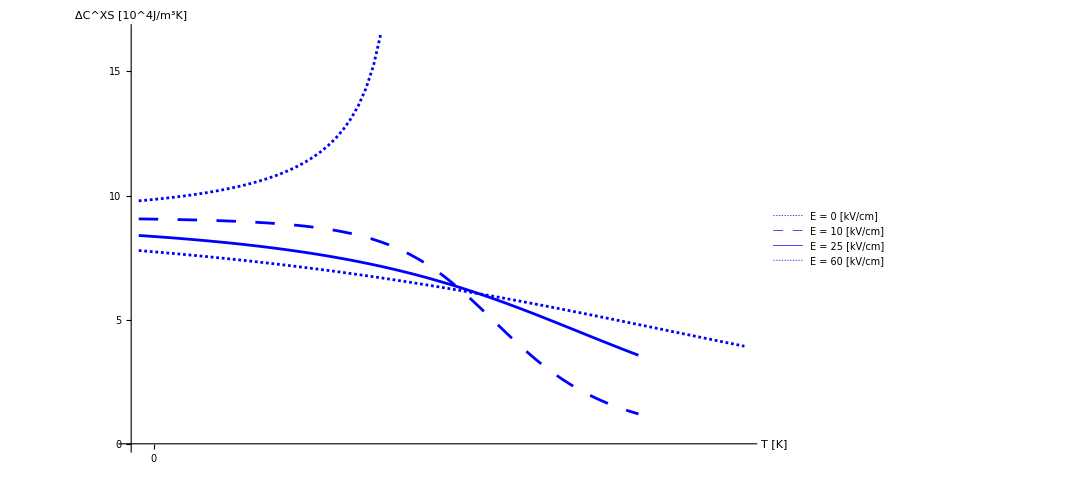

```mathematica
ListLinePlot[{Flatten[Table[ΔCBackward[2,1,k]*10^-4,{k,350,383}]],Flatten[Table[ΔCBackward[2,10,k]*10^-4,{k,350,416}]],Flatten[Table[ΔCBackward[2,26,k]*10^-4,{k,350,416}]],Flatten[Table[ΔCBackward[2,61,k]*10^-4,{k,350,430}]]},AxesLabel->{"T [K]","ΔC^XS [10^4J/m^3K]"},Ticks->{{{3,0},{100,100},{200,200},{300,300},{400,400}},{0,5,10,15,20}},BaseStyle->plotFont,ImageSize->800,PlotStyle->{{Blue,Dashing[Tiny],Thickness[0.0025]},{Blue,Dashing[Large],Thickness[0.0025]},{Blue,Thickness[0.0025]}},PlotLegends->Placed[{"E = 0 [kV/cm]","E = 10 [kV/cm]","E = 25 [kV/cm]","E = 60 [kV/cm]"},{Scaled[{0.15,0.835}],{0.15,0.835}}],LabelStyle->Directive[Black,Bold],AxesOrigin->{0,0}]
```

### VDOS heat capacity + total heat capacity plot:

```mathematica
CvT=Import["/home/john/PSTO_stuff_Byounghak/QPdata/Cv_T_BTO.csv","Data"];Dimensions[CvT]
```

{2000,2}

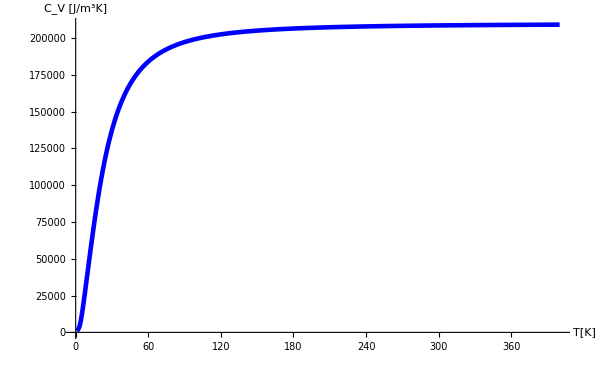

```mathematica
ListLinePlot[Flatten[Table[CvT[[k,2]]/(6.022*10^23 6.430201823999999*^-29),{k,1,400,1}]],ImageSize->600,BaseStyle->{FontWeight->"Bold",FontSize->14},AxesLabel->{"T[K]","C_V [J/m^3K]"},BaseStyle->plotFont,ImageSize->800,PlotStyle->{{Blue,Thickness[0.0055]},{Blue,Dashing[Large],Thickness[0.0025]},{Blue,Thickness[0.0025]}},ImageSize->800,LabelStyle->Directive[Black,Bold],AxesOrigin->{0,0}]
```

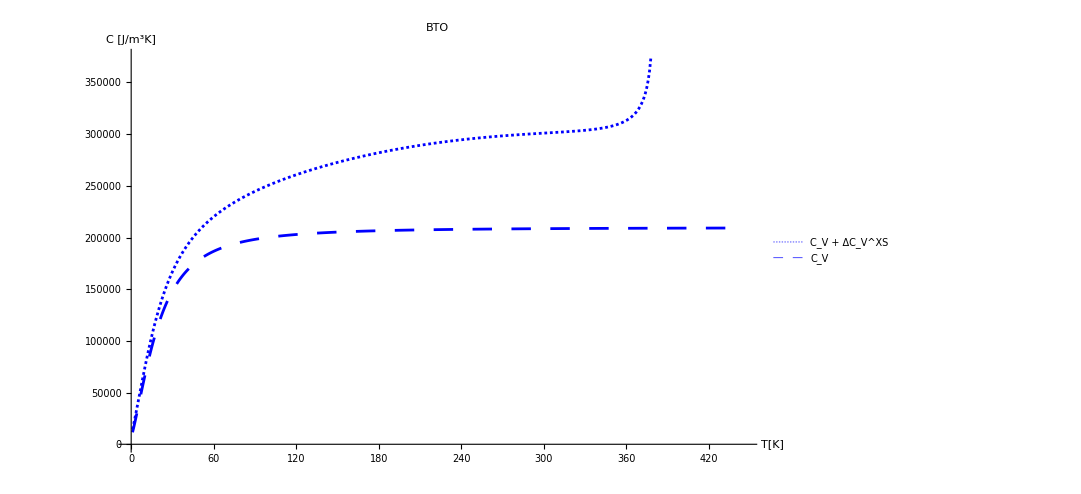

```mathematica
ListLinePlot[{Flatten[Table[{Flatten[CvT[[k,2]]/(6.022*10^23 6.430201823999999*^-29)+ΔCBackward[2,1,k]]},{k,5,390,1}]],Flatten[Table[CvT[[k,2]]/(6.022*10^23 6.430201823999999*^-29),{k,5,450,1}]]},PlotStyle->{{Blue,Dashing[Tiny],Thickness[0.0025]},{Blue,Dashing[Large],Thickness[0.0025]},{Blue,Thickness[0.0025]}},PlotLegends->Placed[{"C_V + ΔC_V^XS","C_V"},{Scaled[{0.08,0.99}],{0.08,0.99}}],BaseStyle->plotFont,AxesLabel->{"T[K]","C [J/m^3K]"},ImageSize->800,PlotLabel->"BTO"]
```

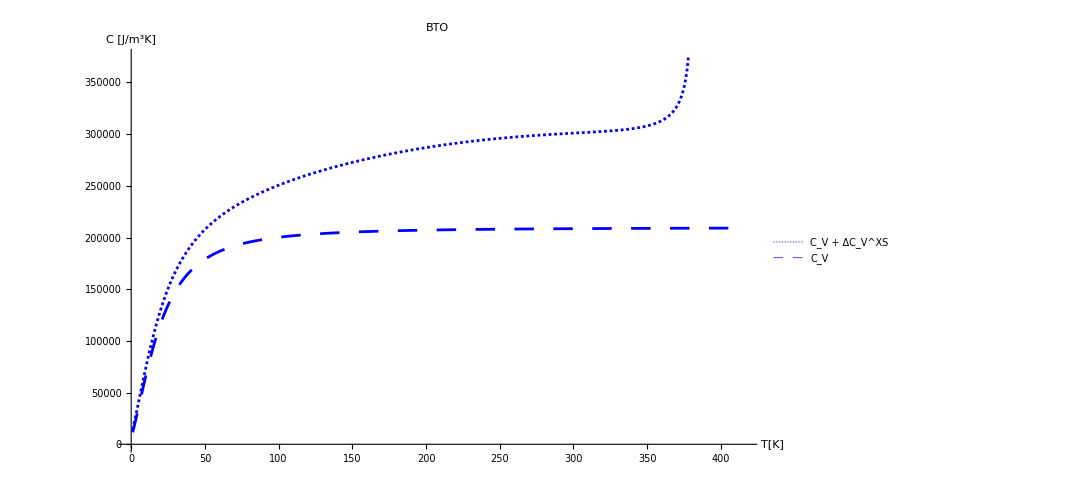

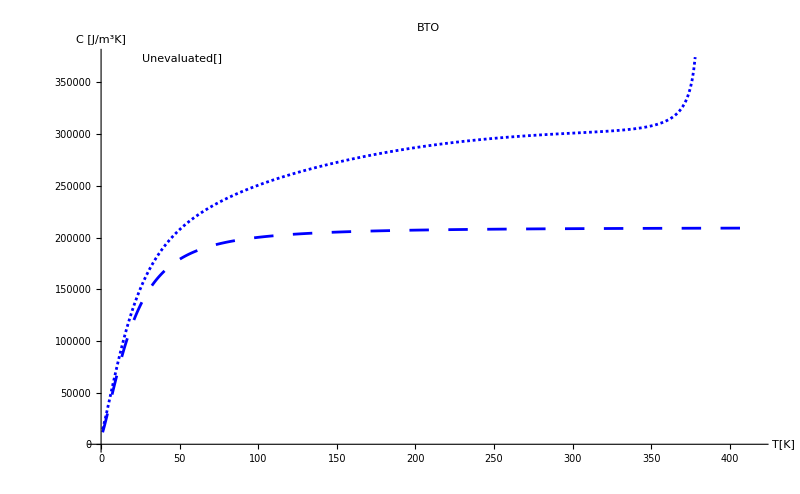

```mathematica
ListLinePlot[{Table[{k,CvT[[k,2]]/(6.022*10^23 6.430201823999999*^-29)+ΔCBackward[2,1,k]},{k,360,390,1}]},ImageSize->600,BaseStyle->{FontWeight->"Bold",FontSize->14},AxesLabel->{"T[K]","C_V + ΔC_V [J/m^3K]"},BaseStyle->plotFont,ImageSize->800,PlotStyle->{{Blue,Dashing[Tiny],Thickness[0.0025]},{Blue,Dashing[Large],Thickness[0.0025]},{Blue,Thickness[0.0025]}},PlotLegends->Placed[{"E = 0 [kV/cm]","E = 10 [kV/cm]","E = 15 [kV/cm]","E = 35 [kV/cm]"},{Scaled[{0.08,0.99}],{0.08,0.99}}],ImageSize->800,LabelStyle->Directive[Black,Bold],AxesOrigin->{0,0}]
```

-Graphics-

## Pyroelectric coefficient:

The pyroelectric coefficient which is defined as (d^2 G)/(d E dT) can be readily approximated as (G[E+h1,T+h2]-G[E+h1,T-h2]-G[E-h1,T+h2]+G[E-h1,T-h2])/(4 h1 h2). It remains to be seen in the PSTO system whether this is the correct approximation. Note that this is a first-order central difference approximation for mixed partials.

```mathematica
p[j_,k_,l_]:=-(1/(4 (0.5*10^5) (1))(G0filmFE[j,k+1,l+1]-G0filmFE[j,k+1,l-1]-G0filmFE[j,k-1,l+1]+G0filmFE[j,k-1,l-1]))
```

Can try to plot this as a surface but that could be something more interesting for PSTO(perhaps with Ex Ey the dependent variables at some fixed temperature near the transition temperature).

More so, it seems that our pyroelectric coefficient is not being approximated properly. 

Why not look at p =dP/dT?

```mathematica
ClearAll[a,b]
```

```mathematica
a[j_,k_,l_]:=P/.Flatten[equilibFE[[j,k,l+1,1]]];
```

```mathematica
b[j_,k_,l_]:=P/.Flatten[equilibFE[[j,k,l,1]]];
```

```mathematica
c[j_,k_,l_]:=P/.Flatten[equilibFE[[j,k,l-1,1]]];
```

```mathematica
d[j_,k_,l_]:=P/.Flatten[equilibFE[[j,k,l+2,1]]];
```

```mathematica
e[j_,k_,l_]:=P/.Flatten[equilibFE[[j,k,l-2,1]]];
```

```mathematica
pyroForward[j_,k_,l_]:=(a[j,k,l]-b[j,k,l])/ϕ
```

```mathematica
pyroBackward[j_,k_,l_]:=(b[j,k,l]-c[j,k,l])/ϕ
```

```mathematica
pyroCentral[j_,k_,l_]:=(a[j,k,l]-c[j,k,l])/(2ϕ)
```

```mathematica
pyroForwardSecond[j_,k_,l_]:=(d[j,k,l]-2a[j,k,l]+b[j,k,l])/ϕ^2
```

```mathematica
pyroCentralSecond[j_,k_,l_]:=(a[j,k,l]-2b[j,k,l]+c[j,k,l])/ϕ^2
```

```mathematica
pyroBackward[2,1,1]
```

Part::partd: Part specification equilibPolFE ⟦ 2, 1, 1, 1 ⟧ is longer than depth of object.

ReplaceAll::reps: {equilibPolFE ⟦ 2, 1, 1, 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification equilibPolFE ⟦ 2, 1, 0, 1 ⟧ is longer than depth of object.

ReplaceAll::reps: {equilibPolFE ⟦ 2, 1, 0, 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-(P/.equilibPolFE⟦2,1,0,1⟧)+(P/.equilibPolFE⟦2,1,1,1⟧)

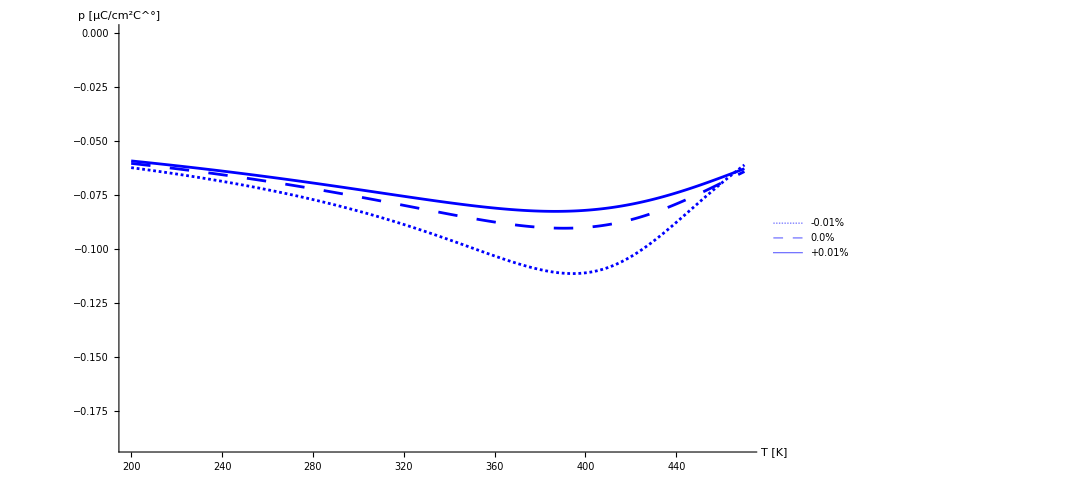

```mathematica
ListLinePlot[{Table[{equilibFE[[1,2,k,3]],100*pyroBackward[2,51,k]},{k,200,470}],Table[{equilibFE[[1,2,k,3]],100*pyroBackward[2,81,k]},{k,200,470}],Table[{equilibFE[[1,2,k,3]],100*pyroBackward[2,100,k]},{k,200,470}]},PlotRange->{-.19,0},ImageSize->800,LabelStyle->Directive[Black,Bold],BaseStyle->plotFont,PlotStyle->{{Blue,Dashing[Tiny],Thickness[0.0025]},{Blue,Dashing[Large],Thickness[0.0025]},{Blue,Thickness[0.0025]}},AxesLabel->{"T [K]","p [μC/cm^2C^°]"},AxesOrigin->{200,0.13},PlotLegends->Placed[{"-0.01%","0.0%","+0.01%"},{Scaled[{0.75,0.435}],{0,0.835}}]](* wierd units for Pamir, 100 times that of SI MKS*)
```

```mathematica
100*pyroBackward[2,1,299] (*this seems to be the right order of magnitude*)
```

-0.0999275

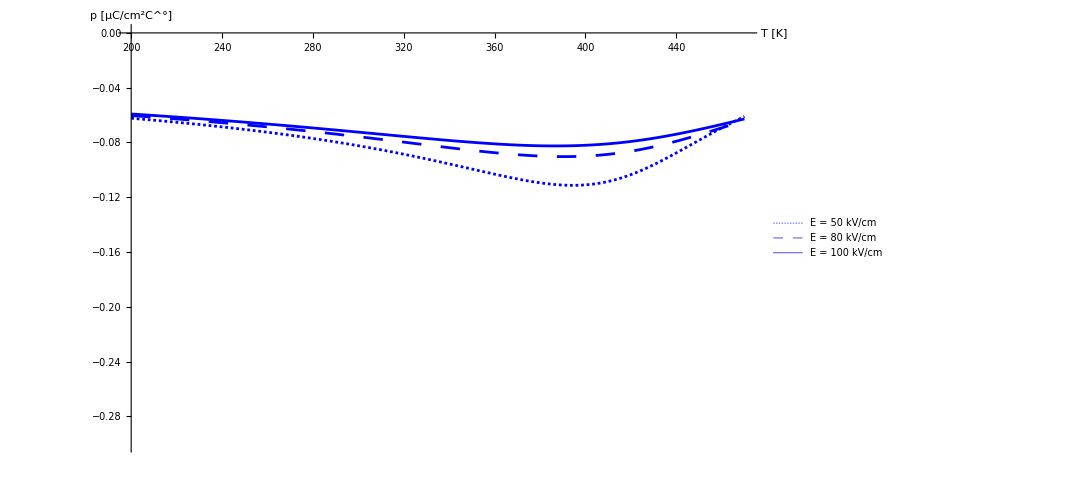

```mathematica
ListLinePlot[{Table[{equilibFE[[1,2,k,3]],100*pyroBackward[2,51,k]},{k,200,470}],Table[{equilibFE[[1,2,k,3]],100*pyroBackward[2,81,k]},{k,200,470}],Table[{equilibFE[[1,2,k,3]],100*pyroBackward[2,100,k]},{k,200,470}]},PlotRange->{-0.3,0.0},ImageSize->800,LabelStyle->Directive[Black,Bold],BaseStyle->plotFont,PlotStyle->{{Blue,Dashing[Tiny],Thickness[0.0025]},{Blue,Dashing[Large],Thickness[0.0025]},{Blue,Thickness[0.0025]}},AxesLabel->{"T [K]","p [μC/cm^2C^°]"},AxesOrigin->{200,0.0},PlotLegends->Placed[{"E = 50 kV/cm","E = 80 kV/cm","E = 100 kV/cm"},{Scaled[{0.65,0.435}],{0,0.835}}]]
```

### Higher order corrections(optional apparently):

It is clear something is wonky here. Let’s use higher order central, forward and backwards differentiation.

```mathematica
pyroForwardHigher[j_,k_,l_]:=(-d[j,k,l]+6a[j,k,l]-3b[j,k,l]-2c[j,k,l])/(6ϕ)
```

```mathematica
pyroBackwardHigher[j_,k_,l_]:=(2a[j,k,l]+3b[j,k,l]-6c[j,k,l]+e[j,k,l])/(6ϕ)
```

```mathematica
pyroCentralHigher[j_,k_,l_]:=(-d[j,k,l]+8a[j,k,l]-8c[j,k,l]+e[j,k,l])/(12ϕ)
```

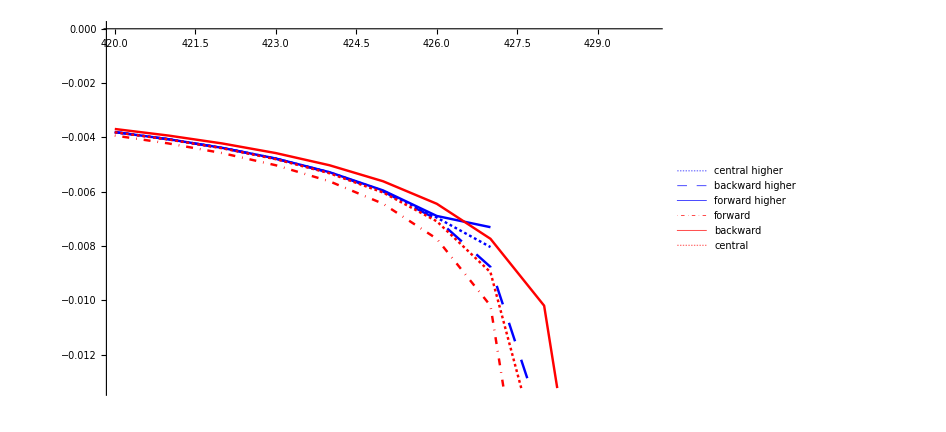

```mathematica
α=420;ListLinePlot[{Table[{equilibPolFE[[1,1,k,3]],pyroCentralHigher[1,1,k]},{k,α,430}],Table[{equilibPolFE[[1,1,k,3]],pyroBackwardHigher[1,1,k]},{k,α,430}],Table[{equilibPolFE[[1,1,k,3]],pyroForwardHigher[1,1,k]},{k,α,430}],Table[{equilibPolFE[[1,1,k,3]],pyroForward[1,1,k]},{k,α,430}],Table[{equilibPolFE[[1,1,k,3]],pyroBackward[1,1,k]},{k,α,430}],Table[{equilibPolFE[[1,1,k,3]],pyroCentral[1,1,k]},{k,α,430}]},PlotLegends->{"central higher","backward higher","forward higher","forward","backward","central"},ImageSize->700,PlotStyle->{{Blue,Dashing[Tiny],Thickness[0.0025]},{Blue,Dashing[Large],Thickness[0.0025]},{Blue,Thickness[0.0025]},{Red,DotDashed,Thickness[0.0025]},{Red,Dot,Thickness[0.0025]},{Red,Dashing[Tiny],Thickness[0.0025]}}]
```

## ΔT (electrocaloric effect):

We now concern ourselves with the following  ΔT(T,E,u_m) = -T (∫^E_b)_E_a 1/(C_(E,u_m))p(T,E,u_m)dE formula for computing the change in temperature due to the change in the applied fields. Since our solutions are discrete we need to rewrite this as a numerical integral or a sum.

```mathematica
ClearAll[TotalHeatCap11,TotalHeatCap12,TotalHeatCap21,TotalHeatCap22,TotalHeatCap31,TotalHeatCap32]
```

This is the issue, we can’t sum all of the temperatures until the intergration. Need to get rid of this step

```mathematica
ΔT1[k_]:=-equilibFE[[1,1,k,3]] Sum[(1/((15*CvT[[k,2]])/(6.022*10^23 6.430201823999999*^-29)+ΔCBackward[1,q,k]))pyroBackward[1,q,k],{q,50,150,1}]
```

```mathematica
ΔT2[k_]:=-equilibFE[[1,1,k,3]] Sum[(1/((15*CvT[[k,2]])/(6.022*10^23 6.430201823999999*^-29)+ΔCBackward[2,q,k]))pyroBackward[2,q,k],{q,50,150,1}]
```

```mathematica
ΔT3[k_]:=-equilibFE[[1,1,k,3]] Sum[(1/((15*CvT[[k,2]])/(6.022*10^23 6.430201823999999*^-29)+ΔCBackward[3,q,k]))pyroBackward[3,q,k],{q,50,150,1}]
```

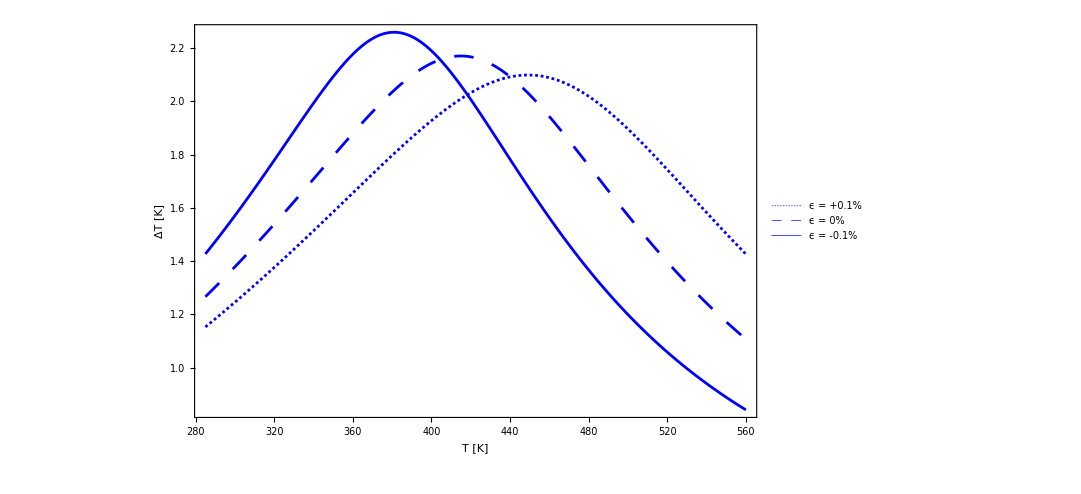

```mathematica
q=ListLinePlot[{Table[Flatten[{equilibFE[[1,1,k,3]],2*10^5*Flatten[ΔT1[k]]}],{k,285,560}],Table[Flatten[{equilibFE[[1,1,k,3]],2*10^5*Flatten[ΔT2[k]]}],{k,285,560}],Table[Flatten[{equilibFE[[1,1,k,3]],2*10^5*Flatten[ΔT3[k]]}],{k,285,560}]},Frame->{True,True,True,True},PlotRangePadding->0,FrameTicksStyle->Directive[Black,18],PlotStyle->{{Blue,Dashing[Tiny],Thickness[0.0025]},{Blue,Dashing[Large],Thickness[0.0025]},{Blue,Thickness[0.0025]}},
PlotLegends->Placed[LineLegend[{Directive[{Blue,Dashing[Tiny],Thickness[0.0025]}],Directive[{Blue,Dashing[Large],Thickness[0.0025]}],Directive[{Blue,Thickness[0.0025]}]},(*can use linelegend with a frame, use Directive on the {Directive[Black,Dashing..],Black,"0","10"} to get hte proper dashing, then use text annotations with the color for strains*)
{Style["ϵ = +0.1%",FontSize->19],
Style["ϵ = 0%",FontSize->19],
Style["ϵ = -0.1%",FontSize->19]
}],{{0.618,0.18},{0.8,0.3}}],
ImageSize->800,FrameLabel->{Style["T [K]",FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->22],Style["ΔT [K]",FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->22]}](*this is approximately equivalent to Pamir's work. Note the CvT needs a factor of 15 on it and the dE needs one more power of 10*)
```

```mathematica
v=ListLinePlot[{Table[Flatten[{equilibFE[[1,1,k,3]],10^5*Flatten[ΔT1[k]]}],{k,285,560}],Table[Flatten[{equilibFE[[1,1,k,3]],10^5*Flatten[ΔT2[k]]}],{k,285,560}],Table[Flatten[{equilibFE[[1,1,k,3]],10^5*Flatten[ΔT3[k]]}],{k,285,560}]},PlotStyle->{{Red,Dashing[Tiny],Thickness[0.0025]},{Red,Dashing[Large],Thickness[0.0025]},{Red,Thickness[0.0025]}},PlotLegends->Placed[{"ϵ = +0.1%","ϵ = 0 %","ϵ = - 0.1%"},{Scaled[{0.78,0.1}],{0.78,0.1}}],ImageSize->800,LabelStyle->Directive[Black,Bold],AxesOrigin->{285,0},AxesLabel->{"T [K]","ΔT [K]"}];
```

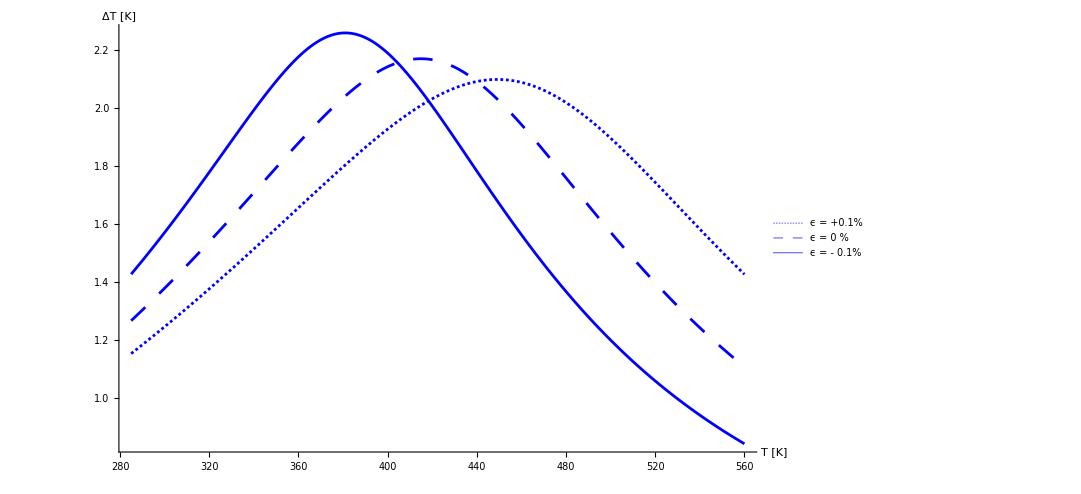

```mathematica
Show[{q},PlotRange->All]
```

factor of 10 seems to be due to Cv being off (need 5 atoms?)

```mathematica
Export["/home/john/solUnstrAllMinSmallFieldPhasEx.csv",solUnstrAllMinSmallFieldPhasEx]
```

/home/john/solUnstrAllMinSmallFieldPhasEx.csv

```mathematica
Export["/home/john/solUnstrAllMinSmallFieldPhasEy.csv",solUnstrAllMinSmallFieldPhasEy]
```

/home/john/solUnstrAllMinSmallFieldPhasEy.csv

```mathematica
Export["/home/john/solUnstrAllMinSmallFieldPhasSame.csv",solUnstrAllMinSmallFieldPhasSame]
```

/home/john/solUnstrAllMinSmallFieldPhasSame.csv

```mathematica
solUnstrAllMinSmallFieldPhasSame
```

```mathematica
2*10^5*Flatten[ΔT1[2]]
```

Part::partd: Part specification {{« 1 »}, {« 1 »}, {{{{{Rule[« 2 »]}}, 0, 1, 0.001}, {{{Rule[« 2 »]}}, 0, 2, 0.001}, {{{Rule[« 2 »]}}, 0, 3, 0.001}, {{{Rule[« 2 »]}}, 0, 4, 0.001}, {{{Rule[« 2 »]}}, 0, 5, 0.001}, {{{Rule[« 2 »]}}, 0, 6, 0.001}, {{{Rule[« 2 »]}}, 0, 7, 0.001}, {{{Rule[« 2 »]}}, 0, 8, 0.001}, « 35 », {{{Rule[« 2 »]}}, 0, 44, 0.001}, {{{Rule[« 2 »]}}, 0, 45, 0.001}, {{{Rule[« 2 »]}}, 0, 46, 0.001}, {{{Rule[« 2 »]}}, 0, 47, 0.001}, {{{Rule[« 2 »]}}, 0, 48, 0.001}, {{{Rule[« 2 »]}}, 0, 49, 0.001}, {{{Rule[« 2 »]}}, 0, 50, 0.001}, « 530 »}, « 49 », « 101 »}} ⟦ « 1 » ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {« 1 » ⟦ 1, 50, 0, 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {« 1 » ⟦ 1, 52, 0, 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted